```mathematica
(*(*MAC*)
dir=NotebookDirectory[]
Join[$Path,{"/opt/anaconda3/bin","/opt/anaconda3/condabin",NotebookDirectory[]}]
SetDirectory[NotebookDirectory[]]
session=StartExternalSession[<|"System"->"Python","Version"->"3.7.6","Executable"->"/opt/anaconda3/bin/python3.7"|>]*)
```

```mathematica
net=Import[NotebookDirectory[]<>"../../../repository/networks/UNETdswResGradientOut_Countnuc_objSz7_crop128Fri_22_May_2020_13-01-34.mx"]["TrainedNet"];
<<AugmentationFunctions`
<<SegmentationV0v1v0`
```

Import::nffil: File /Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/repository/scripts/../../../repository/networks/UNETdswResGradientOut_Countnuc_objSz7_crop128Fri_22_May_2020_13-01-34.mx not found during Import.

```mathematica
files=FileNames["*.tif",NotebookDirectory[]<>"/Trial 1 Max AI",Infinity];
```

```mathematica
(*rescaleTiff[file_,rescaleFac_]:=Module[{metadata,zspacing,xspacing,nucleusChannel},
metadata=Import[file,"Exif"];
If[Not@MissingQ@metadata["XResolution"],
zspacing=ToExpression@StringTake[metadata["ImageDescription"],{Last@Last@StringPosition[metadata["ImageDescription"],"spacing"]+2,Last@Last@StringPosition[metadata["ImageDescription"],"spacing"]+7}];
xspacing=N[1/metadata["XResolution"]];
nucleusChannel=ImageResize[Image3D[removeOutlierpixels@Image3D@Take[Import@file,{1,-1,4}],"Byte"],{Scaled@rescaleFac,Scaled@rescaleFac,Scaled[rescaleFac*zspacing/xspacing]}];
Export[StringTake[file ,;;-5]<>"-RESCALED.tif",nucleusChannel]]]*)
```

```mathematica
(*rescaleTiff[#,1.5]&/@files*)
```

```mathematica
files=FileNames["*RESCALED*.tif",NotebookDirectory[]<>"/Trial 1 Max AI",Infinity]
```

{}

```mathematica
nucsizes=ToExpression[Last[StringSplit[FileBaseName@#,"_"]]]&/@files
```

{20,8,20,20,35,70,20,30}

```mathematica
testimg=Image3D@Import@files[[2]];
```

```mathematica
subtestimg=ImagePad[testimg,-{{500,250},{300,438},{400,50}}]
```

```mathematica
subtestimg=ImagePad[testimg,-{{400,250},{300,400},{400,0}}]
```

```mathematica
(*result=segment3DImageGradientMap[subtestimg,net,7,nucsizes[[2]],.2,"CPU"]*)
```

{16,26,32}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

```mathematica
Colorize@result["segmented"]
```

```mathematica
Image3DSlices[testimg,500]
```

```mathematica
img=ImageResize[Image3D@Import@files[[i]],Scaled[7/20]];
```

```mathematica
Table[
	Export[StringTake[files[[i]],;;-5]<>"_analysed.mx",segment3DImageGradientMap[Image3D@Import@files[[i]],net,7,nucsizes[[i]]]],{i,Length@nucsizes}]
```

{538,538,578}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{672,672,426}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{538,538,296}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{359,331,132}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{307,307,89}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{154,154,186}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{538,538,221}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{358,358,249}

xz slice analysis...

yz slice analysis...

xy slice analysis...

Transposing...

{/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Soft Sox.lif - Series001-RESCALED_size_20_analysed.mx,/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Soft Sox.lif - TileScan 003Series004-RESCALED_size_8_analysed.mx,/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Soft Sox.lif - TileScan 003Series005-RESCALED_size_20_analysed.mx,/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Stiff Sox.lif - Series002-1-RESCALED_size_20_analysed.mx,/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Stiff Sox.lif - Series002-2-RESCALED_size_35_analysed.mx,/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 2/30.8.19 PEG Alveolar 1929 Soft SpC.lif - Series005-RESCALED_size_70_analysed.mx,/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 2/30.8.19 PEG Alveolar 1929 Stiff SpC.lif - Series003-RESCALED_size_20_analysed.mx,/home/fatmax/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/NucCount/Data/Unannotated/VanessaSokleva//Trial 1 Max AI/Set 2/30.8.19 PEG Alveolar 1929 Stiff SpC.lif - Series004-RESCALED_size_30_analysed.mx}

## PostProcessing

```mathematica
analFiles=FileNames["*analysed*","/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI",Infinity]
```

{/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Soft Sox.lif - Series001-RESCALED_size_20_analysed.mx,/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Soft Sox.lif - TileScan 003Series004-RESCALED_size_8_analysed.mx,/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Soft Sox.lif - TileScan 003Series005-RESCALED_size_20_analysed.mx,/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Stiff Sox.lif - Series002-1-RESCALED_size_20_analysed.mx,/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 1/29.7.19 PEG SN Trial 1 Stiff Sox.lif - Series002-2-RESCALED_size_35_analysed.mx,/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 2/30.8.19 PEG Alveolar 1929 Soft SpC.lif - Series005-RESCALED_size_70_analysed.mx,/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 2/30.8.19 PEG Alveolar 1929 Stiff SpC.lif - Series003-RESCALED_size_20_analysed.mx,/Users/MJ 1/Dropbox (Cambridge University)/DeepMirrorLtD/Projects/CytoButler/Data/Nuclei/Unannotated/VanessaSokleva/Trial 1 Max AI/Set 2/30.8.19 PEG Alveolar 1929 Stiff SpC.lif - Series004-RESCALED_size_30_analysed.mx}

```mathematica
results=Map[SparseArray@DeleteSmallComponents[Normal[Import[#]["segmented"]],Round[(7^3)/3]]&,analFiles[[2;;2]]];
```

```mathematica
(*Export[NotebookDirectory[]<>"dump.mx",results]*)
```

```mathematica
(*results=Import[NotebookDirectory[]<>"dump.mx"]*)
```

```mathematica
img=Image3D@Part[ImageData@Import[analFiles[[2]]]["img"],;;150,100;;400,200;;500]
```

```mathematica
Image3D[img,ViewPoint->{2,1,1}]
```

```mathematica
ListAnimate[ImageRotate[img,{#,{0,0,1}}]&/@{0,Pi/4,Pi/2,3*Pi/4}]
```

```mathematica
results[[1]]//Dimensions
```

{426,672,672}

```mathematica
results[[1,;;150,100;;400,200;;500]]//Colorize
```

```mathematica
nucsizes
```

{20,8,20,20,35,70,20,30}

```mathematica
elong=Map[Last/@ComponentMeasurements[#,"Elongation"]&,results];
```

```mathematica
centroids=Map[Last/@ComponentMeasurements[#,"Centroid"]&,results];
```

NearestFunction[{3, <>}]

```mathematica
EuclideanDistance
```

{{32.8969,528.927,576.477},{33.5989,527.896,571.885},{28.9065,534.923,574.598},{33.3563,521.102,573.913},{29.48,535.307,569.02}}

```mathematica
EuclideanDistance[nf[centroids[[1,1]],5][[3]],centroids[[1,1]]]
```

7.4431

{32.8969,528.927,576.477}

```mathematica
getDistances[centroids_]:=
```

```mathematica
dm=DistanceMatrix/@centroids;
```

```mathematica
d=Median/@Map[Median[Rest[Sort[#][[;;6]]]]&,dm,{2}]
```

{8.90206,10.4112,14.5446,8.16742,8.89938,11.9569,9.18114,10.2635}

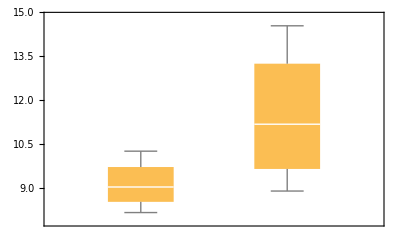

```mathematica
BoxWhiskerChart@{Last/@Select[Transpose@{FileBaseName/@analFiles,d},StringContainsQ[First@#,"Stiff"]&],
Last/@Select[Transpose@{FileBaseName/@analFiles,d},StringContainsQ[First@#,"Soft"]&]}
```

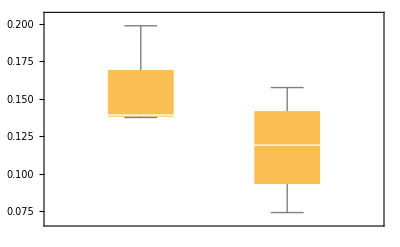

```mathematica
BoxWhiskerChart@{Last/@Select[Transpose@{FileBaseName/@analFiles,Mean/@elong},StringContainsQ[First@#,"Stiff"]&],
Last/@Select[Transpose@{FileBaseName/@analFiles,Mean/@elong},StringContainsQ[First@#,"Soft"]&]}
```

```mathematica
Near
```

```mathematica
Map[Last,GatherBy[Transpose@{FileBaseName/@analFiles,Mean/@Map[Last,feats,{2}]},StringTake[First@#,8]&],{2}]
```

{{0.0740865,0.12604,0.112037,0.137446,0.198542},{0.157384,0.13966,0.13847}}

```mathematica
elong=Map[Last,feats,{2}];
```

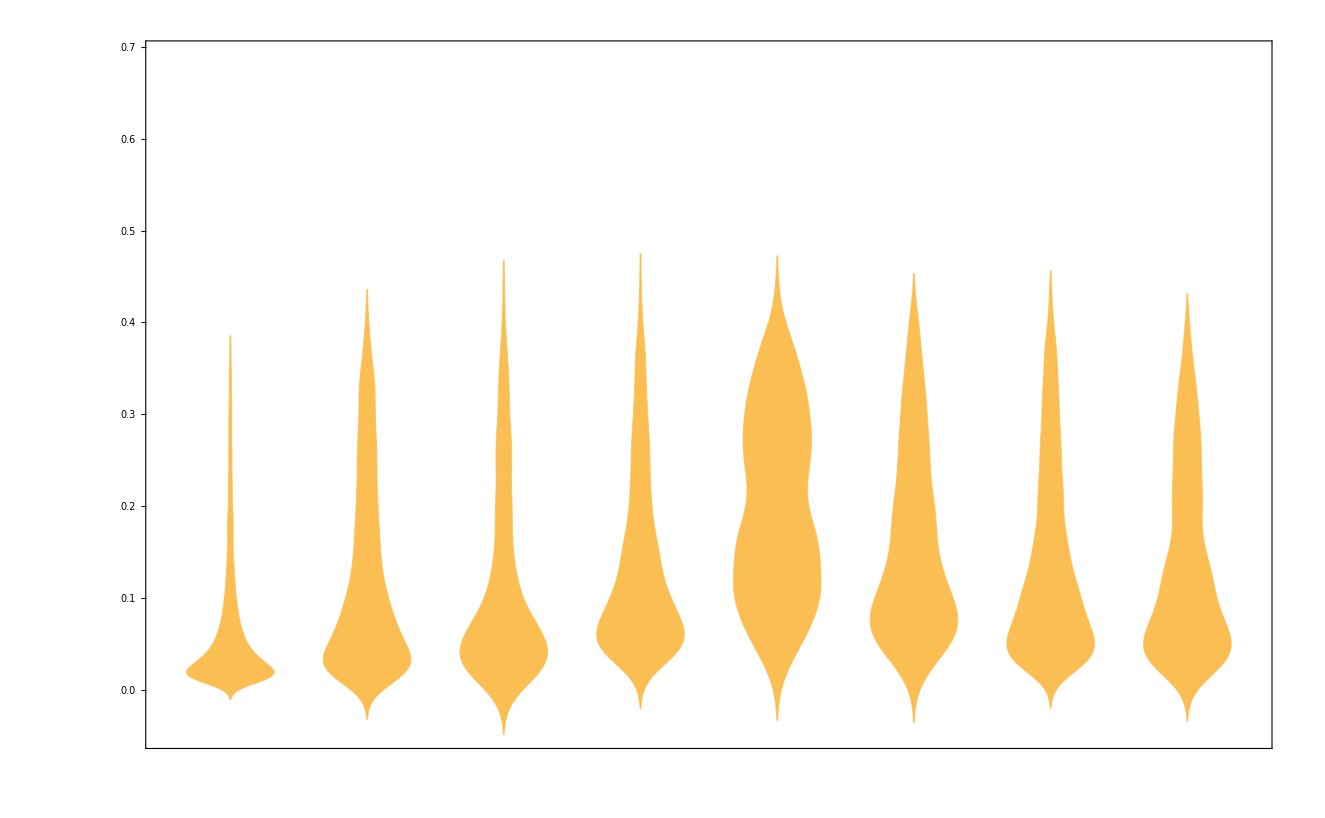

```mathematica
DistributionChart@elong
```

```mathematica
netevaluateGradNet[ImageResize[Image3DSlices[testimg,400,3],Scaled[7/20]],net,"GPU"]
```

<|pmap→-Graphics-,horzGrad→-Graphics-,vertGrad→-Graphics-|>

```mathematica
Colorize@result["segmented"][[450]]
```